```mathematica
homeDir=$HomeDirectory;
desktopDirectory=homeDir<>"\\Desktop\\";
fdaDirectory=desktopDirectory<>"Surrogates\\";
pathSVM=desktopDirectory<>"SVM\\"
outputDir=desktopDirectory<>"\\Surrogates\\SmallHemorrhage\\"
nb1=fdaDirectory<>"librarySmall-header.nb";
nb=NotebookOpen[nb1];
SelectionMove[nb,All,Notebook];
SelectionEvaluate[nb];
NotebookClose[nb];
parms=Flatten[Import[outputDir<>"parmList.txt","CSV"]];
rawvars=Import[outputDir<>"HemSmallRoster.Script","Text"];
varRoster=StringSplit[StringSplit[StringReplace[rawvars,{"<roster>"->"","</roster>"->"","<var><name>"->"","\n\n"->"\n","</name>"->"","</var>"->""," "->""}],"\n"],"<format>"][[All,1]]
p[x_,y_]:=Less[ToExpression[StringSplit[x,{".","_"}][[2]]],ToExpression[StringSplit[y,{".","_"}][[2]]]]
```

C:\Users\HL\Desktop\SVM\

C:\Users\HL\Desktop\\Surrogates\SmallHemorrhage\

{System.X,FluidVolumes.ECFV,FluidVolumes.BV,FluidVolumes.AP,FluidVolumes.UO,BaroreceptorReflex.SYM,BaroreceptorReflex.AFFNA,CardiacOutput.MCFP,CardiacOutput.RAP,CardiacOutput.CO,CardiacOutput.RVR,FlowAutoregulation.TPR}

```mathematica
SetDirectory[outputDir<>"data\\"]
DataOut=Map[ToExpression,Import["SAData.csv"]];
samples=Map[ToExpression,Import["SASamples.csv"]];

limitX={14469,14471};
limitECFV={10000,20000};
limitBV={3000,7000};
limitAP={75,200};
limitCO={2000,7000};


limits={Interval[limitX],Interval[limitECFV],Interval[limitBV],Interval[limitAP],Interval[limitCO]};
(*limits={Interval[limitX],Interval[limitMAP],Interval[limitCO],Interval[limitAldo],Interval[limitADH],Interval[limitANP],Interval[limitNa],Interval[limitGFR]};*)
dataout=DataOut;
FullData=Table[{samples[[i]],dataout[[i,1]],dataout[[i,2]]},{i,Length[dataout]}];
FullData=Select[FullData,Union[{IntervalMemberQ[limits[[1]],#[[-1,1]]],IntervalMemberQ[limits[[2]],#[[2,2]]],IntervalMemberQ[limits[[3]],#[[2,3]]],IntervalMemberQ[limits[[4]],#[[2,4]]],IntervalMemberQ[limits[[5]],#[[2,10]]]}]=={True}&];
diffList=FullData[[All,2,4]]-FullData[[All,3,4]];
fullData=Map[Flatten,Table[{FullData[[i]],{diffList[[i]]}},{i,1,Length[diffList]}]];

modeldata=FullData[[All,2;;3]][[1;;200]];
samples=FullData[[All,1]][[1;;200]];
parms={"BaroreceptorReflex.SYMFXD","BaroreceptorReflex.AffNaA","BaroreceptorReflex.AffNam","BaroreceptorReflex.AffNaS","BaroreceptorReflex.SympsA","BaroreceptorReflex.Sympsm","BaroreceptorReflex.SympsS","BaroreceptorReflex.SympsB","CardiacOutput.V0","CardiacOutput.slope_a","CardiacOutput.slope_b","CardiacOutput.SlopeB","CardiacOutput.HSBasic","CardiacOutput.StarlingA","CardiacOutput.Starlingm","CardiacOutput.StarlingS","CardiacOutput.RVRa","CardiacOutput.RVRb","FlowAutoregulation.AutoA","FlowAutoregulation.Autom","FlowAutoregulation.AutoS","FluidVolumes.Intake","FluidVolumes.Urinem","FluidVolumes.FluidA","FluidVolumes.Fluidm","FluidVolumes.FluidS"};
Ranges={{0.925,1.075},{1.9425,2.2575},{3.35775,3.90225},{46.25,53.75},{0.9435,1.0965},{3.22825,3.75175},{0.49025,0.56975},{1.0545,1.2255},{3080.25,3579.75},{0.3182,0.3698},{0.6,0.697675},{0.006475,0.007525},{0.925,1.075},{6937.5,8062.5},{1.7353,2.0167},{2.63625,3.06375},{0.032375,0.037625},{0.000592,0.000688},{0.0419025,0.0486975},{10.0455,11.6745},{4741.55,5510.45},{0.925,1.075},{0.04625,0.05375},{7307.5,8492.5},{3.3115,3.8485},{14402.25,16737.75}}
spl=parms;
```

C:\Users\HL\Desktop\Surrogates\SmallHemorrhage\data

{{0.925,1.075},{1.9425,2.2575},{3.35775,3.90225},{46.25,53.75},{0.9435,1.0965},{3.22825,3.75175},{0.49025,0.56975},{1.0545,1.2255},{3080.25,3579.75},{0.3182,0.3698},{0.6,0.697675},{0.006475,0.007525},{0.925,1.075},{6937.5,8062.5},{1.7353,2.0167},{2.63625,3.06375},{0.032375,0.037625},{0.000592,0.000688},{0.0419025,0.0486975},{10.0455,11.6745},{4741.55,5510.45},{0.925,1.075},{0.04625,0.05375},{7307.5,8492.5},{3.3115,3.8485},{14402.3,16737.8}}

BaroreceptorReflex.SYMFXD | 0.599411 | 1.20525
BaroreceptorReflex.AffNaA | 2.37982 | 0.813913
BaroreceptorReflex.AffNam | 0.636969 | 0.485062
BaroreceptorReflex.AffNaS | 4.97069 | 2.16648
BaroreceptorReflex.SympsA | 0.532713 | 0.52847
BaroreceptorReflex.Sympsm | 1.60637 | 0.826973
BaroreceptorReflex.SympsS | 1.62566 | 1.6136
BaroreceptorReflex.SympsB | 2.74302 | 2.01352
CardiacOutput.V0 | 9.16241 | 3.92688
CardiacOutput.slope_a | 10.5092 | 0.801281
CardiacOutput.slope_b | 2.4496 | 0.755262
CardiacOutput.SlopeB | 1.89396 | 5.30915
CardiacOutput.HSBasic | 2.10247 | 0.354373
CardiacOutput.StarlingA | 2.17845 | 1.47075
CardiacOutput.Starlingm | 6.48327 | 0.623277
CardiacOutput.StarlingS | 0.421636 | 0.339654
CardiacOutput.RVRa | 16.1178 | 0.339921
CardiacOutput.RVRb | 0.276914 | 1.4876
FlowAutoregulation.AutoA | 2.04427 | 2.03424
FlowAutoregulation.Autom | 2.4833 | 1.57858
FlowAutoregulation.AutoS | 16.0097 | 2.83733
FluidVolumes.Intake | 8.56186 | 0.81948
FluidVolumes.Urinem | 26.8575 | 1.10852
FluidVolumes.FluidA | 6.00915 | 1.59472
FluidVolumes.Fluidm | 1.76928 | 1.16361
FluidVolumes.FluidS | 0.895113 | 1.85767

{{BaroreceptorReflex.SYMFXD,1},{BaroreceptorReflex.AffNaA,14},{BaroreceptorReflex.AffNam,4},{BaroreceptorReflex.AffNaS,10},{BaroreceptorReflex.SympsA,0},{BaroreceptorReflex.Sympsm,7},{BaroreceptorReflex.SympsS,15},{BaroreceptorReflex.SympsB,13},{CardiacOutput.V0,62},{CardiacOutput.slope_a,17},{CardiacOutput.slope_b,5},{CardiacOutput.SlopeB,6},{CardiacOutput.HSBasic,5},{CardiacOutput.StarlingA,17},{CardiacOutput.Starlingm,13},{CardiacOutput.StarlingS,1},{CardiacOutput.RVRa,22},{CardiacOutput.RVRb,1},{FlowAutoregulation.AutoA,10},{FlowAutoregulation.Autom,12},{FlowAutoregulation.AutoS,90},{FluidVolumes.Intake,15},{FluidVolumes.Urinem,41},{FluidVolumes.FluidA,25},{FluidVolumes.Fluidm,8},{FluidVolumes.FluidS,14}}

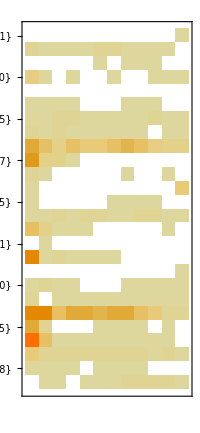

```mathematica
Mu=Mean[samples];
Sig=StandardDeviation[samples];
closePos[ints_,i_,x_]:=Flatten[Position[Map[IntervalMemberQ[ints[[i]],#]&,x[[All,i]]],True]]
farPos[ints_,i_,x_]:=Complement[Range[Length[x]],closePos[ints,i,x]]
Checks={2,3,4,10};
reducedData=modeldata[[All,1,Checks]];
redMu=N[Mean[reducedData]];
redSig=N[StandardDeviation[reducedData]];
normedData=Map[(#-redMu)/redSig&,reducedData];

delList={0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0,1.25,1.5};
FirstOrderVariances={};


For[j=1,j≤Length[delList],j++,
del=delList[[j]];
temp={};
ints=Map[Interval,Transpose[{Mu-del*Sig,Mu+del*Sig}]];
For[i=1,i≤Length[samples[[1]]],i++,
fv=Variance[normedData[[farPos[ints,i,samples]]]];
cv=Variance[normedData[[closePos[ints,i,samples]]]];
AppendTo[temp,fv/cv]]
AppendTo[FirstOrderVariances,Apply[Times,temp,2]]]
TableForm[Transpose[{spl,FirstOrderVariances[[1]],FirstOrderVariances[[-1]]}]]

tfFOV=Ceiling[FirstOrderVariances-1.2];
yticks=Transpose[{spl,Map[Total,Transpose[tfFOV]]}]
ticks=Transpose[{Range[Length[spl]],yticks}];
tticks=Transpose[{Range[delList],delList}];
MatrixPlot[Transpose[tfFOV],FrameTicks->{ticks,None}]
```

```mathematica
(* sensitives is the list of sensitive parameters, where (parm, n) represents the parameter name and the number of speilon for which it was above the sensitivity threshold*)
sensitives=Select[Transpose[{spl,Map[Total,Transpose[tfFOV]]}],#[[2]]>14&]
sensParms=sensitives[[All,1]];
sensPos=Flatten[Map[Position[spl,#]&,sensParms]];
sensRanges=Ranges[[sensPos]];
```

{{BaroreceptorReflex.SympsS,15},{CardiacOutput.V0,62},{CardiacOutput.slope_a,17},{CardiacOutput.StarlingA,17},{CardiacOutput.RVRa,22},{FlowAutoregulation.AutoS,90},{FluidVolumes.Intake,15},{FluidVolumes.Urinem,41},{FluidVolumes.FluidA,25}}

```mathematica
(* I am excluding the sampling and running aspects of the software suite.  Contact me if you would like them separately*)
SetDirectory[outputDir<>"PrimerData\\"]
fn=Sort[FileNames[],p[#1,#2]&];
DataOut=Drop[Import[#,"CSV"]&/@fn,0,0,-1];
```

C:\Users\HL\Desktop\Surrogates\SmallHemorrhage\PrimerData

```mathematica
newsamples=Map[ToExpression,Import[outputDir<>"Run2.CSV","CSV"]];
limitX={14444,14446};
limitECFV={10000,20000};
limitBV={3000,7000};
limitAP={75,200};
limitCO={2000,7000};

limits={Interval[limitX],Interval[limitECFV],Interval[limitBV],Interval[limitAP],Interval[limitCO]};
(*limits={Interval[limitX],Interval[limitMAP],Interval[limitCO],Interval[limitAldo],Interval[limitADH],Interval[limitANP],Interval[limitNa],Interval[limitGFR]};*)
dataout=DataOut;
FullData=Table[{newsamples[[i]],dataout[[i,1]],dataout[[i,2]]},{i,Length[dataout]}];
FullData=Select[FullData,Union[{IntervalMemberQ[limits[[1]],#[[-1,1]]],IntervalMemberQ[limits[[2]],#[[2,2]]],IntervalMemberQ[limits[[3]],#[[2,3]]],IntervalMemberQ[limits[[4]],#[[2,4]]],IntervalMemberQ[limits[[5]],#[[2,10]]]}]=={True}&];
diffList=FullData[[All,2,4]]-FullData[[All,3,4]];
fullData=Map[Flatten,Table[{FullData[[i]],{diffList[[i]]}},{i,1,Length[diffList]}]];

modeldata=FullData[[All,2;;3]];
samples=FullData[[All,1]];
spl=sensParms;

mup=Map[Mean,Transpose[samples]];
sigp=Map[StandardDeviation,Transpose[samples]];
rangeList=Transpose[{mup-2sigp,mup+2*sigp}];
```

```mathematica
indexOfInterest=4;
cList={100};
gList={.01};

For[ind1=1,ind1≤Length[cList],ind1++,
For[ind2=1,ind2≤Length[gList],ind2++,
cc=cList[[ind1]];
gg=gList[[ind2]];
generatePopulationModels[1000,indexOfInterest,modeldata,samples,varRoster,False];
Print[{cc,gg,StandardDeviation[error]}]]]
```

{100,0.01,2.38799}

{{3.65862,2.90289,2.95694,2.87743,2.76844,2.80655},{4.2224,3.02675,3.21774,2.70938,2.71959,2.62267},{3.18124,2.78552,2.93151,3.05966,2.77898,2.91822}}

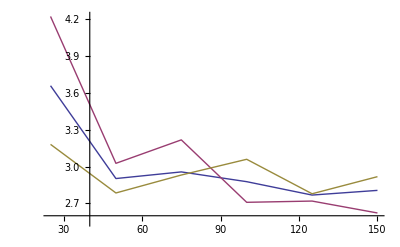

```mathematica
(*Figure 1*)
teL=Transpose[errorList]
smallerrors=Transpose[Insert[teL,NList,1]];
list1=smallerrors[[All,1;;2]];
list2=smallerrors[[All,{1,3}]];
list3=smallerrors[[All,{1,4}]];
ListPlot[{list1,list2,list3},Joined->True]
```

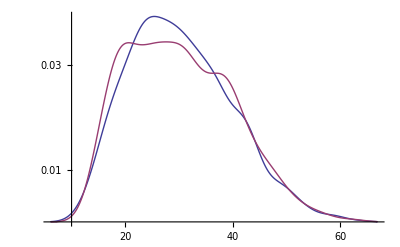

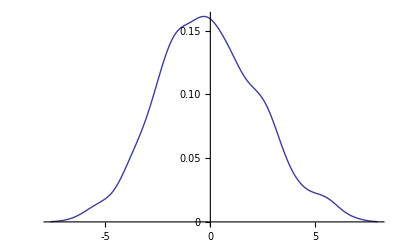

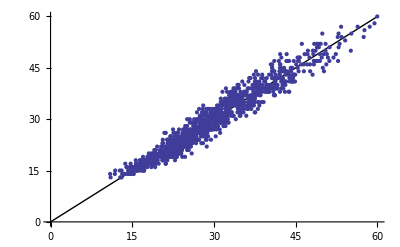

```mathematica
(*Figure 2*)
SmoothHistogram[{dt,loutput}]
SmoothHistogram[error]
errorData=Transpose[{dt,loutput}];
Show[Plot[x,{x,0,60},PlotStyle->{Black,Thick}],ListPlot[errorData]]
```

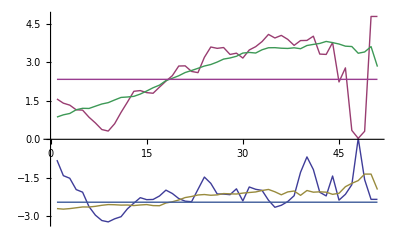

```mathematica
(*Figure 3*)
T=Sort[Transpose[{loutput,dt}]];

rollingWindow[x_,xi_]:=Module[{ind},
X=x[[All,1]];
m=Min[X];
M=Max[X];
window={};
For[ind=m,ind≤M,ind++,
temp=Select[x,IntervalMemberQ[Interval[{ind-xi,ind+xi}],#[[1]]]&];
dtemp=temp[[All,1]]-temp[[All,2]];
If[Length[dtemp]>1,
AppendTo[window,{Mean[dtemp],StandardDeviation[dtemp]}],
AppendTo[window,{Mean[dtemp],0}]]];
Return[window]];

view[w_]:={w[[All,1]]-w[[All,2]],w[[All,1]]+w[[All,2]]};
jList={1,10,100};
views=Table[view[rollingWindow[T,jList[[j]]]],{j,1,Length[jList]}];
ListPlot[Flatten[views,1],Joined->True]
```

```mathematica
(*different n levels*)
NList={25,50,75,100,125,150}
errorList={};
For[NNN=1,NNN≤Length[NList],NNN++,
templist={};
Do[
nnn=NList[[NNN]];
cc=100;
gg=0.01;
generatePopulationModels[nnn,indexOfInterest,modeldata,samples,varRoster,False];
AppendTo[templist,StandardDeviation[error]],{3}];
AppendTo[errorList,templist]]
```

{25,50,75,100,125,150}

```mathematica
teL=Transpose[errorList]
smallerrors=Transpose[Insert[teL,NList,1]];
list1=smallerrors[[All,1;;2]];
list2=smallerrors[[All,{1,3}]];
list3=smallerrors[[All,{1,4}]];
ListPlot[{list1,list2,list3},Joined->True]
```

{{3.65862,2.90289,2.95694,2.87743,2.76844,2.80655},{4.2224,3.02675,3.21774,2.70938,2.71959,2.62267},{3.18124,2.78552,2.93151,3.05966,2.77898,2.91822}}

-Graphics-